## A Tree base

We define a function to see if a graph is a broken cycle, meaning it has all edges around the cyle except between “the first and the last vertex”

```mathematica
BrokenCycleQ[g_]:=Block[{},
VertexCount[g]==1||
Fold[And,Table[EdgeQ[g,n->n+1],{n,1,VertexCount[g]-1}]]
]
```

First non zero gives the first index in a vector that is not zero

```mathematica
FirstNonZero[vect_]:=Block[{result=1,k},
For[k=1,k≤Length[vect],k++,
If[vect[[k]]≠0, Return [result], result++]
];
result
]
```

```mathematica
all6TreeKeys=Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]}, TreeGraphQ[g] ] &];
```

```mathematica
allGraphs6TreeKeys=Sort[
Select[all6TreeKeys,BrokenCycleQ[allGraphs6[#,"graph"]]&],FirstNonZero[BaseCoeff[#1,"C"]]<FirstNonZero[BaseCoeff[#2,"C"]]&];
```

```mathematica
Table[allGraphs6[k,"colotree"]=PartitionToSymbol[allGraphs6[k,"vertexsets"],"t"],{k,allGraphs6TreeKeys}]
```

{t123456,t12345x6,t1234x5x6,t12346x5,t1234x56,t123x4x5x6,t123x4x56,t1236x4x5,t123x46x5,t1235x4x6,t12356x4,t1235x46,t123x45x6,t1236x45,t123x456,t12x3x4x5x6,t12x3x4x56,t12x3x46x5,t12x3x45x6,t12x3x456,t126x3x4x5,t126x3x45,t12x36x4x5,t12x36x45,t125x3x4x6,t125x3x46,t1256x3x4,t125x36x4,t12x35x4x6,t12x35x46,t126x35x4,t12x356x4,t124x3x5x6,t124x3x56,t1246x3x5,t124x36x5,t1245x3x6,t12456x3,t1245x36,t124x35x6,t1246x35,t124x356,t12x34x5x6,t12x34x56,t126x34x5,t12x346x5,t125x34x6,t1256x34,t125x346,t12x345x6,t126x345,t12x3456,t1x2x3x4x5x6,t1x2x3x4x56,t1x2x3x46x5,t1x2x3x45x6,t1x2x3x456,t1x2x36x4x5,t1x2x36x45,t1x2x35x4x6,t1x2x35x46,t1x2x356x4,t1x2x34x5x6,t1x2x34x56,t1x2x346x5,t1x2x345x6,t1x2x3456,t16x2x3x4x5,t16x2x3x45,t16x2x35x4,t16x2x34x5,t16x2x345,t1x26x3x4x5,t1x26x3x45,t1x26x35x4,t1x26x34x5,t1x26x345,t15x2x3x4x6,t15x2x3x46,t15x2x36x4,t15x2x34x6,t15x2x346,t156x2x3x4,t156x2x34,t15x26x3x4,t15x26x34,t1x25x3x4x6,t1x25x3x46,t1x25x36x4,t1x25x34x6,t1x25x346,t16x25x3x4,t16x25x34,t1x256x3x4,t1x256x34,t14x2x3x5x6,t14x2x3x56,t14x2x36x5,t14x2x35x6,t14x2x356,t146x2x3x5,t146x2x35,t14x26x3x5,t14x26x35,t145x2x3x6,t145x2x36,t1456x2x3,t145x26x3,t14x25x3x6,t14x25x36,t146x25x3,t14x256x3,t1x24x3x5x6,t1x24x3x56,t1x24x36x5,t1x24x35x6,t1x24x356,t16x24x3x5,t16x24x35,t1x246x3x5,t1x246x35,t15x24x3x6,t15x24x36,t156x24x3,t15x246x3,t1x245x3x6,t1x245x36,t16x245x3,t1x2456x3,t13x2x4x5x6,t13x2x4x56,t13x2x46x5,t13x2x45x6,t13x2x456,t136x2x4x5,t136x2x45,t13x26x4x5,t13x26x45,t135x2x4x6,t135x2x46,t1356x2x4,t135x26x4,t13x25x4x6,t13x25x46,t136x25x4,t13x256x4,t134x2x5x6,t134x2x56,t1346x2x5,t134x26x5,t1345x2x6,t13456x2,t1345x26,t134x25x6,t1346x25,t134x256,t13x24x5x6,t13x24x56,t136x24x5,t13x246x5,t135x24x6,t1356x24,t135x246,t13x245x6,t136x245,t13x2456,t1x23x4x5x6,t1x23x4x56,t1x23x46x5,t1x23x45x6,t1x23x456,t16x23x4x5,t16x23x45,t1x236x4x5,t1x236x45,t15x23x4x6,t15x23x46,t156x23x4,t15x236x4,t1x235x4x6,t1x235x46,t16x235x4,t1x2356x4,t14x23x5x6,t14x23x56,t146x23x5,t14x236x5,t145x23x6,t1456x23,t145x236,t14x235x6,t146x235,t14x2356,t1x234x5x6,t1x234x56,t16x234x5,t1x2346x5,t15x234x6,t156x234,t15x2346,t1x2345x6,t16x2345,t1x23456}

```mathematica
repFullToTree=ToRules[
Reduce[
Table[
allGraphs6[k,"colotree"]==allGraphs6[k,"colofour"]
,
{k,allGraphs6TreeKeys}
],
Table[allGraphs6[k,"colofour"],{k,allGraphs6AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs6[k,"colotree"]=Simplify[allGraphs6[k,"colofour"]/.repFullToTree],
{k,Sort[Keys[allGraphs6]]}
],k];
```

```mathematica
vars=Sort[Table[PartitionToSymbol[allGraphs6[k,"vertexsets"],"t"],{k,allGraphs6TreeKeys}],CompareSymbols]
```

{t1x2x3x4x5x6,t1x2x3x4x56,t1x2x3x45x6,t1x2x3x46x5,t1x2x34x5x6,t1x2x35x4x6,t1x2x36x4x5,t1x23x4x5x6,t1x24x3x5x6,t1x25x3x4x6,t1x26x3x4x5,t12x3x4x5x6,t13x2x4x5x6,t14x2x3x5x6,t15x2x3x4x6,t16x2x3x4x5,t1x2x34x56,t1x2x35x46,t1x2x36x45,t1x23x4x56,t1x23x45x6,t1x23x46x5,t1x24x3x56,t1x24x35x6,t1x24x36x5,t1x25x3x46,t1x25x34x6,t1x25x36x4,t1x26x3x45,t1x26x34x5,t1x26x35x4,t12x3x4x56,t12x3x45x6,t12x3x46x5,t12x34x5x6,t12x35x4x6,t12x36x4x5,t13x2x4x56,t13x2x45x6,t13x2x46x5,t13x24x5x6,t13x25x4x6,t13x26x4x5,t14x2x3x56,t14x2x35x6,t14x2x36x5,t14x23x5x6,t14x25x3x6,t14x26x3x5,t15x2x3x46,t15x2x34x6,t15x2x36x4,t15x23x4x6,t15x24x3x6,t15x26x3x4,t16x2x3x45,t16x2x34x5,t16x2x35x4,t16x23x4x5,t16x24x3x5,t16x25x3x4,t1x2x3x456,t1x2x345x6,t1x2x346x5,t1x2x356x4,t1x234x5x6,t1x235x4x6,t1x236x4x5,t1x245x3x6,t1x246x3x5,t1x256x3x4,t123x4x5x6,t124x3x5x6,t125x3x4x6,t126x3x4x5,t134x2x5x6,t135x2x4x6,t136x2x4x5,t145x2x3x6,t146x2x3x5,t156x2x3x4,t12x34x56,t12x35x46,t12x36x45,t13x24x56,t13x25x46,t13x26x45,t14x23x56,t14x25x36,t14x26x35,t15x23x46,t15x24x36,t15x26x34,t16x23x45,t16x24x35,t16x25x34,t1x23x456,t1x234x56,t1x235x46,t1x236x45,t1x24x356,t1x245x36,t1x246x35,t1x25x346,t1x256x34,t1x26x345,t12x3x456,t12x345x6,t12x346x5,t12x356x4,t123x4x56,t123x45x6,t123x46x5,t124x3x56,t124x35x6,t124x36x5,t125x3x46,t125x34x6,t125x36x4,t126x3x45,t126x34x5,t126x35x4,t13x2x456,t13x245x6,t13x246x5,t13x256x4,t134x2x56,t134x25x6,t134x26x5,t135x2x46,t135x24x6,t135x26x4,t136x2x45,t136x24x5,t136x25x4,t14x2x356,t14x235x6,t14x236x5,t14x256x3,t145x2x36,t145x23x6,t145x26x3,t146x2x35,t146x23x5,t146x25x3,t15x2x346,t15x234x6,t15x236x4,t15x246x3,t156x2x34,t156x23x4,t156x24x3,t16x2x345,t16x234x5,t16x235x4,t16x245x3,t1x2x3456,t1x2345x6,t1x2346x5,t1x2356x4,t1x2456x3,t1234x5x6,t1235x4x6,t1236x4x5,t1245x3x6,t1246x3x5,t1256x3x4,t1345x2x6,t1346x2x5,t1356x2x4,t1456x2x3,t123x456,t124x356,t125x346,t126x345,t134x256,t135x246,t136x245,t145x236,t146x235,t156x234,t12x3456,t1234x56,t1235x46,t1236x45,t1245x36,t1246x35,t1256x34,t13x2456,t1345x26,t1346x25,t1356x24,t14x2356,t1456x23,t15x2346,t16x2345,t1x23456,t12345x6,t12346x5,t12356x4,t12456x3,t13456x2,t123456}

```mathematica
BaseCoeff6[key_]:=Table[Coefficient[allGraphs6[key,"colotree"],var],{var,vars}]
```

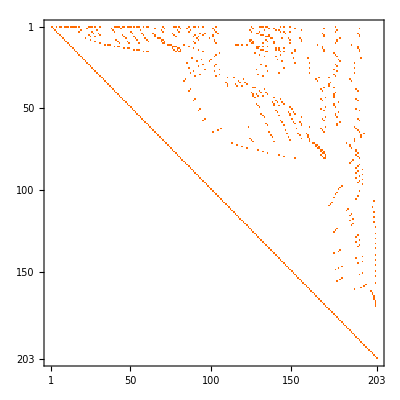

```mathematica
Table[BaseCoeff6[k],{k,allGraphs6AtomKeys}]//Sort//Reverse//Inverse//MatrixPlot
```

```mathematica
Flatten[Table[BaseCoeff6[k],{k,allGraphs6AtomKeys}]]//Tally//Sort
```

{{-6,20},{-2,10},{-1,385},{0,40395},{1,263},{2,135},{24,1}}

```mathematica
Total[Flatten[ConversionMatrix["E","C"]-ConversionMatrix["E","T"]]]
```

131

```mathematica
Total[Flatten[ConversionMatrix["E","C"]]]
```

358

```mathematica
Total[Flatten[ConversionMatrix["E","T"]]]
```

227

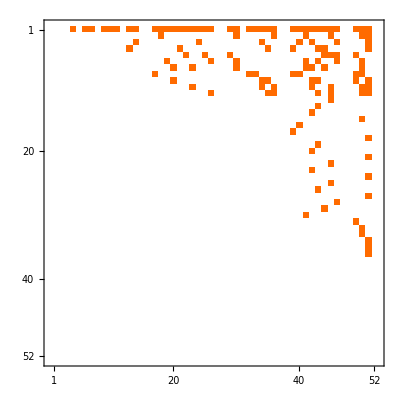

```mathematica
MatrixPlot[ConversionMatrix["E","C"]-ConversionMatrix["E","T"]]
```

```mathematica
SetPartitions[Range[5]]
```

{{{1,2,3,4,5}},{{1},{2,3,4,5}},{{1,2},{3,4,5}},{{1,3,4,5},{2}},{{1,2,3},{4,5}},{{1,4,5},{2,3}},{{1,2,4,5},{3}},{{1,3},{2,4,5}},{{1,2,3,4},{5}},{{1,5},{2,3,4}},{{1,2,5},{3,4}},{{1,3,4},{2,5}},{{1,2,3,5},{4}},{{1,4},{2,3,5}},{{1,2,4},{3,5}},{{1,3,5},{2,4}},{{1},{2},{3,4,5}},{{1},{2,3},{4,5}},{{1},{2,4,5},{3}},{{1},{2,3,4},{5}},{{1},{2,5},{3,4}},{{1},{2,3,5},{4}},{{1},{2,4},{3,5}},{{1,2},{3},{4,5}},{{1,3},{2},{4,5}},{{1,4,5},{2},{3}},{{1,2},{3,4},{5}},{{1,3,4},{2},{5}},{{1,5},{2},{3,4}},{{1,2},{3,5},{4}},{{1,3,5},{2},{4}},{{1,4},{2},{3,5}},{{1,2,3},{4},{5}},{{1,4},{2,3},{5}},{{1,5},{2,3},{4}},{{1,2,4},{3},{5}},{{1,3},{2,4},{5}},{{1,5},{2,4},{3}},{{1,2,5},{3},{4}},{{1,3},{2,5},{4}},{{1,4},{2,5},{3}},{{1},{2},{3},{4,5}},{{1},{2},{3,4},{5}},{{1},{2},{3,5},{4}},{{1},{2,3},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2,5},{3},{4}},{{1,2},{3},{4},{5}},{{1,3},{2},{4},{5}},{{1,4},{2},{3},{5}},{{1,5},{2},{3},{4}},{{1},{2},{3},{4},{5}}}

```mathematica
CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
c1=StringCount[str1,"x"];
c2=StringCount[str2,"x"];
If[c1≠c2,
Greater[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]
```

```mathematica
Table[Labeled[ShowGraph5Least[k],Rotate[Style[SymbolToLabel2[allGraphs5[k,"colotree"]],Red,10],Pi/2],Right],{k,Sort[allGraphs5TreeKeys,!CompareSymbols[allGraphs5[#1,"colotree"],allGraphs5[#2,"colotree"]]&]}]
```

{-Graphics-590481OverHat[0],-Graphics-30586115♁234,-Graphics-326841145♁23,-Graphics-31984014♁235,-Graphics-368980135♁24,-Graphics-3901411345,-Graphics-383080134♁25,-Graphics-36194013♁245,-Graphics-499721125♁34,-Graphics-5223211245,-Graphics-514780124♁35,-Graphics-5677011235,-Graphics-5828811234,-Graphics-560121123♁45,-Graphics-49220112♁345,-Graphics-2988812345,-Graphics-23770115♁24,-Graphics-28308215♁23,-Graphics-21510215♁34,-Graphics-258682145,-Graphics-25168014♁25,-Graphics-31224114♁23,-Graphics-24414114♁35,-Graphics-346201135,-Graphics-375481134,-Graphics-33916013♁25,-Graphics-35434013♁24,-Graphics-33158113♁45,-Graphics-476942125,-Graphics-507181124,-Graphics-552522123,-Graphics-46942112♁35,-Graphics-48460212♁34,-Graphics-46184212♁45,-Graphics-20812125♁34,-Graphics-230721245,-Graphics-22318024♁35,-Graphics-276101235,-Graphics-291282234,-Graphics-26852223♁45,-Graphics-200602345,-Graphics-21420315,-Graphics-24384214,-Graphics-33130113,-Graphics-46180312,-Graphics-20721225,-Graphics-22287124,-Graphics-26821323,-Graphics-19969235,-Graphics-20029334,-Graphics-19940345,-Graphics-199365OverHat[1]}